NOTE: MOST OF THE ANSWERS ARE SOLVED BY PUTTING THE VALUES IN THE CODES GIVEN BY THE PROFESSSOR
question no 1 :

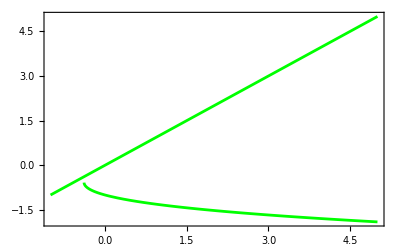

```mathematica
slopevec = {(1/e)((a-v) (v-1) v -w), b v - ɣ w +c};
statevec = {v,w};
parmvec = {a,b, c, e, ɣ};
parmval = {-1,0.12, 0, 1, 0.12};
fixedpoints[stv_,slv_,slw_]:= 
	Solve[Table[(slv[[jj]]/.slw)==0,{jj,1,Length[stv]}],stv]
Solve[slopevec[[1]]==0,v];
Solve[slopevec[[2]]==0,v];
nc1 = (Solve[slopevec[[1]]==0,v] /. Thread[parmvec -> parmval])[[1,1]];
pl1=Plot[v/.nc1,{w,-1,5},Frame->True,PlotStyle->{AbsoluteThickness[2],Green},PlotRange->All];
nc2 = (Solve[slopevec[[2]]==0,v] /. Thread[parmvec -> parmval])[[1,1]];
pl2=Plot[v/.nc2,{w,-1,5},Frame->True,PlotStyle->{AbsoluteThickness[2],Green},PlotRange->All];
plx1=Show[pl1,pl2]
```

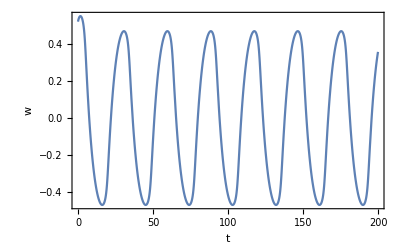

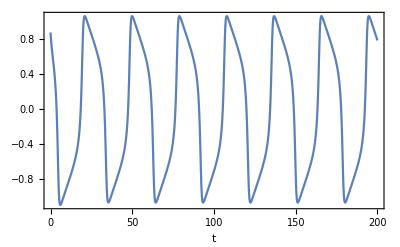

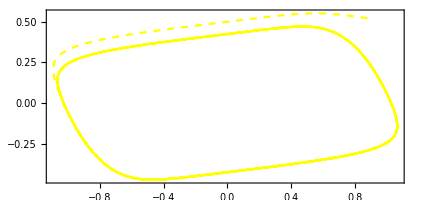

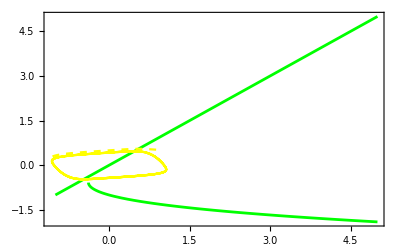

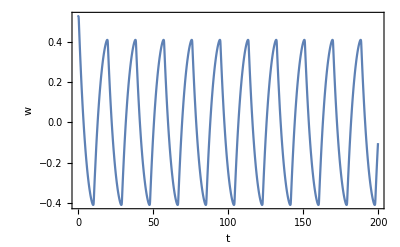

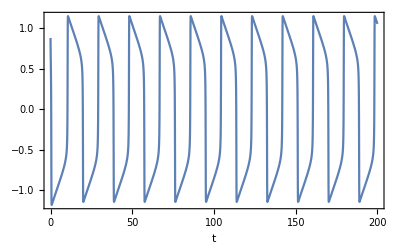

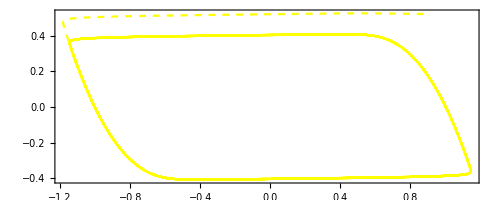

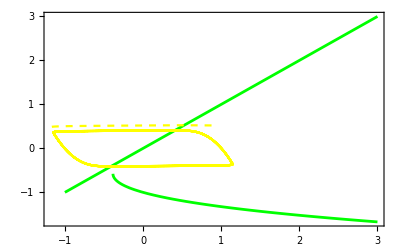

```mathematica
timeIndex=600;
v0[v_,w_]:=(1/e)((a-v[t]) (v[t]-1) v[t] -w[t]);
v00[v_,w_]:=b v[t] - ɣ w[t] +c;
SeedRandom[1234];
sys0=Flatten[{{D[v[1][t], t]==v0[v[1],w[1]],D[w[1][t], t]==v00[v[1],w[1]],v[1][0]==RandomReal[],w[1][0]==RandomReal[]}}];
subst1 = { a->-1,b->0.12, c->0, e->1,ɣ ->0.12} ;
subst2 = { a->-1,b->0.12, c->0, e->0.1, ɣ->0.12} ;
var0 = {v[1],w[1]};

replSingle = NDSolve[ Evaluate[sys0 /. subst1], var0, {t, 0, timeIndex},
Method->"ExplicitRungeKutta",
MaxSteps -> 120000,
AccuracyGoal -> 6,
PrecisionGoal->9];
pl3=Plot[(w[1][t]/.subst1/.replSingle)[[1]],{t,0,200},Frame->True, AxesLabel->{"t","w"}]

pl4=Plot[(v[1][t]/.subst1/.replSingle)[[1]],{t,0,200},Frame->True, AxesLabel->Automatic]
pl5=ParametricPlot[{(v[1][t]/.subst1/.replSingle)⟦1⟧,(w[1][t]/.subst1/.replSingle)⟦1⟧},{t,0,200},Frame->True,PlotPoints->200, PlotStyle->{Dashed,Yellow}]

plx1Full = Show[plx1,pl5]

replSingle = NDSolve[ Evaluate[sys0 /. subst2], var0, {t, 0, timeIndex},
Method->"ExplicitRungeKutta",
MaxSteps -> 120000,
AccuracyGoal -> 6,
PrecisionGoal->9];

pl6=Plot[(w[1][t]/.subst2/.replSingle)[[1]],{t,0,200},Frame->True,FrameLabel->{"t","w"}]

pl7=Plot[(v[1][t]/.subst2/.replSingle)[[1]],{t,0,200},Frame->True, FrameLabel->Automatic]
pl8=ParametricPlot[{(v[1][t]/.subst2/.replSingle)⟦1⟧,(w[1][t]/.subst2/.replSingle)⟦1⟧},{t,0,200},Frame->True,PlotPoints->200,PlotStyle->{Dashed,Yellow}]
parmval2 = {-1,0.12, 0, 0.1, 0.12};
nc3 = (Solve[slopevec[[1]]==0,v] /. Thread[parmvec -> parmval2])[[1,1]];
pl31=Plot[v/.nc3,{w,-1,3},Frame->True,PlotStyle->{AbsoluteThickness[2],Green},PlotRange->All];
nc4 = (Solve[slopevec[[2]]==0,v] /. Thread[parmvec -> parmval2])[[1,1]];
pl41=Plot[v/.nc4,{w,-1,3},Frame->True,PlotStyle->{AbsoluteThickness[2],Green},PlotRange->All];
plx2=Show[pl31,pl41];
plx2Full = Show[plx2,pl8]
```

question no 2 :

NDSolve::ndstf: At t == 155.734, system appears to be stiff. Methods Automatic, BDF, or StiffnessSwitching may be more appropriate.

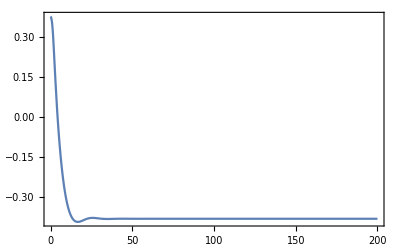

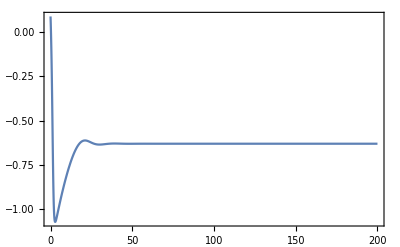

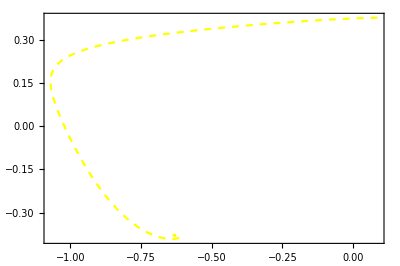

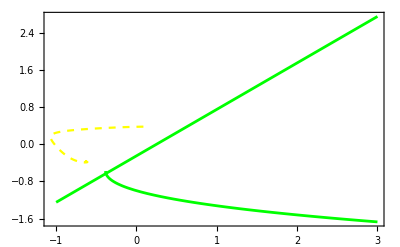

```mathematica
subst3 = { a->-1,b->0.12, c->0.03, e->1, ɣ->0.12} ;
parmval3 = {-1,0.12, 0.03, 1, 0.12};

ncn1= (Solve[slopevec[[1]]==0,v] /.Thread[parmvec -> parmval3])[[1,1]];
pln1=Plot[v/.ncn1,{w,-1,3},Frame->True,PlotStyle->{AbsoluteThickness[2],Green},PlotRange->All];
ncn2 = (Solve[slopevec[[2]]==0,v] /.Thread[parmvec -> parmval3])[[1,1]];
pln2=Plot[v/.ncn2,{w,-1,3},Frame->True,PlotStyle->{AbsoluteThickness[2],Green},PlotRange->All];
plx=Show[pln1,pln2];
sys0=Flatten[{{D[v[1][t], t]==v0[v[1],w[1]],D[w[1][t], t]==v00[v[1],w[1]],v[1][0]==RandomReal[],w[1][0]==RandomReal[]}}];
subst1 = { a->-1,b->0.12, c->0, e->1, ɣ->0.12} ;
subst2 = { a->-1,b->0.12, c->0, e->0.1, ɣ->0.12} ;
var0 = {v[1],w[1]};
replSingle = NDSolve[ Evaluate[sys0 /. subst3], var0, {t, 0, timeIndex},
Method->"ExplicitRungeKutta",
MaxSteps -> 120000,
AccuracyGoal -> 6,
PrecisionGoal->9];
plt1=Plot[(w[1][t]/.subst3/.replSingle)[[1]],{t,0,200},Frame->True, PlotRange->All]
plt2=Plot[(v[1][t]/.subst3/.replSingle)[[1]],{t,0,200},Frame->True,PlotRange->All]
pltp=ParametricPlot[{(v[1][t]/.subst3/.replSingle)⟦1⟧,(w[1][t]/.subst3/.replSingle)⟦1⟧},{t,0,600},Frame->True,PlotPoints->200,PlotStyle->{Dashed,Yellow},PlotRange->All]
Show[plx,pltp]
```

```mathematica
fp1 = fixedpoints[statevec,slopevec,subst3];
fp1/.Thread[parmvec->parmval3];
fp1[[1]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{v→-0.629961,w→-0.379961}

NDSolve::ndstf: At t == 142.852, system appears to be stiff. Methods Automatic, BDF, or StiffnessSwitching may be more appropriate.

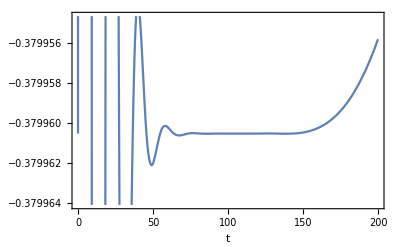

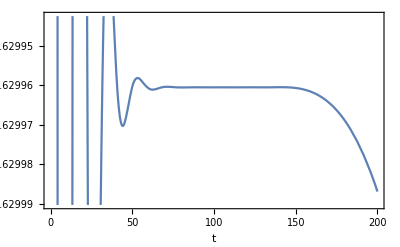

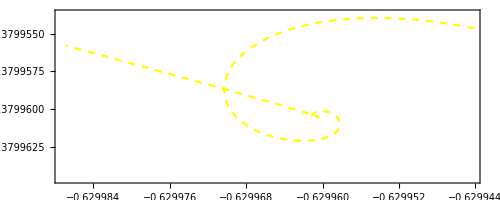

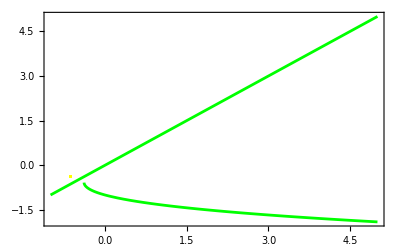

```mathematica
sys0=Flatten[{{D[v[1][t], t]==v0[v[1],w[1]],D[w[1][t], t]==v00[v[1],w[1]],v[1][0]==fp1[[1,1,2]]+0.01,w[1][0]==fp1[[1,2,2]]}}];
subst1 = { a->-1,b->0.12, c->0, e->1, ɣ->0.12} ;
subst2 = { a->-1,b->0.12, c->0, e->0.1, ɣ->0.12} ;
var0 = {v[1],w[1]};
subst1 = { a->-1,b->0.12, c->0, e->1,ɣ->0.12} ;
subst2 = { a->-1,b->0.12, c->0, e->0.1, ɣ->0.12} ;
var0 = {v[1],w[1]};
replSingle = NDSolve[ Evaluate[sys0 /. subst3], var0, {t, 0, timeIndex},
Method->"ExplicitRungeKutta",
MaxSteps -> 120000,
AccuracyGoal -> 6,
PrecisionGoal->9];

pl3=Plot[(w[1][t]/.subst3/.replSingle)[[1]],{t,0,200},Frame->True, AxesLabel->{"t","w"}]

pl4=Plot[(v[1][t]/.subst3/.replSingle)[[1]],{t,0,200},Frame->True, AxesLabel->Automatic]
pl5=ParametricPlot[{(v[1][t]/.subst3/.replSingle)⟦1⟧,(w[1][t]/.subst3/.replSingle)⟦1⟧},{t,0,200},Frame->True,PlotPoints->200, PlotStyle->{Dashed,Yellow}]

plx1Full = Show[plx1,pl5]
```

NDSolve::ndstf: At t == 192.838, system appears to be stiff. Methods Automatic, BDF, or StiffnessSwitching may be more appropriate.

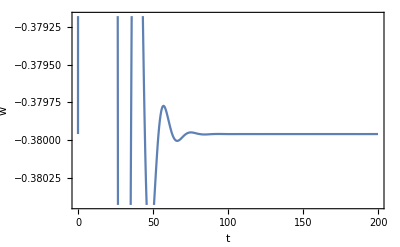

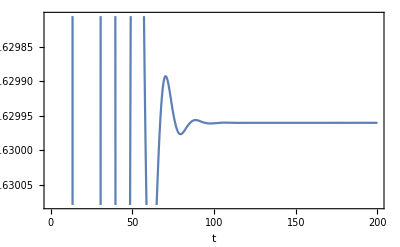

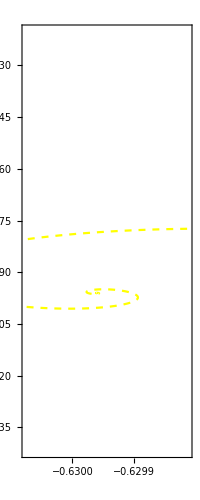

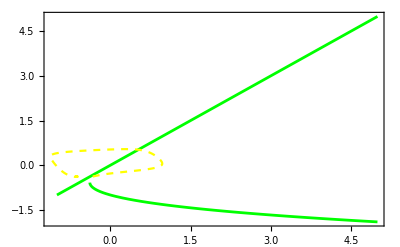

```mathematica
sys0=Flatten[{{D[v[1][t], t]==v0[v[1],w[1]],D[w[1][t], t]==v00[v[1],w[1]],v[1][0]==fp1[[1,1,2]]+0.3,w[1][0]==fp1[[1,2,2]]}}];
subst1 = { a->-1,b->0.12, c->0, e->1, ɣ->0.12} ;
subst2 = { a->-1,b->0.12, c->0, e->0.1, ɣ->0.12} ;
var0 = {v[1],w[1]};
subst1 = { a->-1,b->0.12, c->0, e->1, ɣ->0.12} ;
subst2 = { a->-1,b->0.12, c->0, e->0.1, ɣ->0.12} ;
var0 = {v[1],w[1]};
replSingle = NDSolve[ Evaluate[sys0 /. subst3], var0, {t, 0, timeIndex},
Method->"ExplicitRungeKutta",
MaxSteps -> 120000,
AccuracyGoal -> 6,
PrecisionGoal->9];

pl3=Plot[(w[1][t]/.subst3/.replSingle)[[1]],{t,0,200},Frame->True, AxesLabel->{"t","w"}]

pl4=Plot[(v[1][t]/.subst3/.replSingle)[[1]],{t,0,200},Frame->True, AxesLabel->Automatic]
pl5=ParametricPlot[{(v[1][t]/.subst3/.replSingle)⟦1⟧,(w[1][t]/.subst3/.replSingle)⟦1⟧},{t,0,200},Frame->True,PlotPoints->200, PlotStyle->{Dashed,Yellow}]

plx1Full = Show[plx1,pl5]
```

```mathematica
question no 3:
```

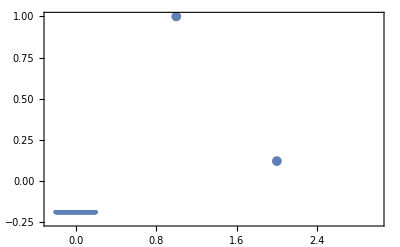

```mathematica
subst4 = { a->-1,b->0.12, c->0, e->1, ɣ->0.12} ;
parmvec14={a,b,e};
parmval14= {-1, 0.12, 1};
jacobian[stv_,slv_]:= Table[D[slv[[i]],stv[[j]]],{i,1,Length[stv]},
	{j,1,Length[stv]}]
jac1 = jacobian[statevec,slopevec];
jac1 // MatrixForm;
(jac1/.fp1[[1]])//MatrixForm;
matP1 = (jac1 /. fp1[[1]]) /. Thread[parmvec14-> parmval14];
Eigenvalues[matP1];
evFull = Eigenvalues[jac1/.fp1[[1]]];
tab = Table[{c,ɣ/. Chop[FindRoot[(Re[evFull[[1]]]==0)/.Thread[parmvec14->parmval14], {ɣ,0.01},PrecisionGoal->5]]},{c, -0.2,0.2,0.001}];
evPl2 = ListPlot[Evaluate[{Reverse[parmval14]}],PlotStyle-> {AbsolutePointSize[7], Green}];
evPl1 = ListPlot[tab,Frame->True,PlotRange->{{-0.25,3},{-0.25,1}}];

Show[evPl1,evPl2]
```

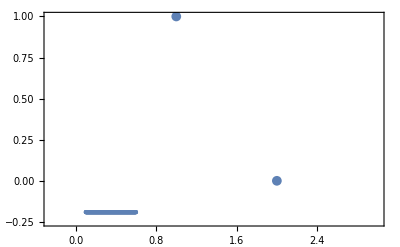

```mathematica
subst4 = { a->-1,b->0.12, c->0, e->1, ɣ->0.12} ;
parmvec14={a,c,e};
parmval14= {-1, 0, 1};
jacobian[stv_,slv_]:= Table[D[slv[[i]],stv[[j]]],{i,1,Length[stv]},
	{j,1,Length[stv]}]
jac1 = jacobian[statevec,slopevec];
jac1 // MatrixForm;
(jac1/.fp1[[1]])//MatrixForm;
matP1 = (jac1 /. fp1[[1]]) /. Thread[parmvec14-> parmval14];
Eigenvalues[matP1];
evFull = Eigenvalues[jac1/.fp1[[1]]];
tab = Table[{b,ɣ /. Chop[FindRoot[(Re[evFull[[1]]]==0)/.Thread[parmvec14->parmval14], {ɣ,0.01},PrecisionGoal->5]]},{b, 0.1,0.6,0.001}];
evPl2 = ListPlot[Evaluate[{Reverse[parmval14]}],PlotStyle-> {AbsolutePointSize[7], Green}];
evPl1 = ListPlot[tab,Frame->True,PlotRange->{{-0.25,3},{-0.25,1}}];

Show[evPl1,evPl2]
```